```mathematica
ClearAll[E1, E2, E3, z]
```

```mathematica
n1=1.500;
n2=1.500;
n3=1.500;
w1=40;
w2=60;
w3=w1+w2;
k1=n1 w1/c;
k2=n2 w2/c;
k3=n3 w3/c;
c=1;
X2=0.01;
Δk= k3-k2-k1

equations={D[E3[z],z]==- I w3/(2 c n3) X2 E1[z]*E2[z] Exp[I Δk z],D[E2[z],z]==-I w2/(2 c n2) X2 E3[z]*Conjugate[E1[z]] Exp[I Δk z], D[E1[z],z]==- I w1/(2 c n1) X2 E3[z]*Conjugate[E2[z]] Exp[I Δk z]};
initials= {E3[0]==0, E1[0]==1/Sqrt[4], E2[0]==Sqrt[3/4]};
```

0.

```mathematica
s=NDSolve[{equations, initials}, {E1[z], E2[z], E3[z]}, {z,0,100}];
```

```mathematica
E1=Abs[E1[z]]/.s;
E2=Abs[E2[z]]/.s;
E3=Abs[E3[z]]/.s;
```

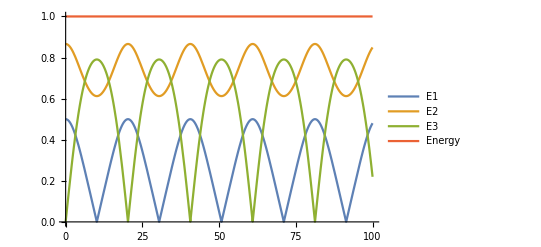

```mathematica
Plot[{E1, E2, E3, E1^2+E2^2+E3^2 }, {z, 0,100}, PlotLegends->{"E1","E2","E3", "Energy"}]
```